```mathematica
"Here we have a return amplitude of the form (NNN)^(-h).  To compute the probablity amplitudes we need the Lanczos coefficients and derivatives of the return amplitude (at a desired point in time).  To compute the derivative I have found it more efficient to compute deriviates of NNN and plug it into an expression for the general derivative of (F(t))^(-h).  There may be ways to do this even faster though"
```

```mathematica
"Here is a test function - analytic results are possible for this so we can compare it with known expressions"
```

```mathematica
varSub = {h->1, c->1/2, ω->1/3};   NNN =Cos[ω t] + I c/ω Sin[ω t];  ReturnAmpt = NNN^(-h)/.varSub;  NNNNum = NNN/.varSub;    Genf =  F[t]^(-h)/.varSub;
```

```mathematica
"To compute the Lanczos coefficients we need a package called Combinatrica which contains the function "
```

```mathematica
Needs["Combinatorica`"]
```

```mathematica
"nnn denotes the number of derivatives we will be taking - the number of Lanczos coefficients one generates is nnn/2.  This loop here computes the Lanczos coefficients via the moments method"
```

```mathematica
Clear[ϕn, NNND, NNNDTab, ϕt, PPlot];
```

```mathematica
nnn = 74; NNNn = Simplify[Series[ReturnAmpt, {t, 0, nnn} ]]; μTab = Table[Factorial[j]SeriesCoefficient[ NNNn, j], {j, 0, nnn}];  MijR = Simplify[   Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ]; bProd = Table[Det[MijR[[1;;k, 1;;k]]      ]/Det[MijR[[1;;(k-1), 1;;(k-1)]]      ], {k, 2, nnn/2+1}];   bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    aTab = Table[Simplify[   -I(    Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]]   ] -    If[k > 2, Simplify[   Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]]   ]  , 0])   ]  , {k, 2, Length[bTab]}   ];
```

```mathematica
aTab
```

{1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2,21/2,23/2,25/2,27/2,29/2,31/2,33/2,35/2,37/2,39/2,41/2,43/2,45/2,47/2,49/2,51/2,53/2,55/2,57/2,59/2,61/2,63/2,65/2,67/2,69/2,71/2}

```mathematica
bTab
```

{(√5)/6,(√5)/3,(√5)/2,(2 √5)/3,(5 √5)/6,√5,(7 √5)/6,(4 √5)/3,(3 √5)/2,(5 √5)/3,(11 √5)/6,2 √5,(13 √5)/6,(7 √5)/3,(5 √5)/2,(8 √5)/3,(17 √5)/6,3 √5,(19 √5)/6,(10 √5)/3,(7 √5)/2,(11 √5)/3,(23 √5)/6,4 √5,(25 √5)/6,(13 √5)/3,(9 √5)/2,(14 √5)/3,(29 √5)/6,5 √5,(31 √5)/6,(16 √5)/3,(11 √5)/2,(17 √5)/3,(35 √5)/6,6 √5,(37 √5)/6}

```mathematica
aTab={3.,0.,-0.857143,-0.53869,2.20553,-0.935853,-0.223874,-0.519827,0.0218167};bTab={2.,2.64575,2.79942,2.03347,2.21273,1.05864,1.13677,1.5512,0.508354};
```

```mathematica
"Here we compute the derivatives at a set of desired points in time.  ϕPts is the number of probabiliyt amplitudes wanted - this should be less than the number of Lanczos coefficients"
```

```mathematica
tMax = 10;   tPts = 100;  ϕPts = 23;   tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], 200];
```

```mathematica
"Here the derivatives are computed at the time-points.  "
```

```mathematica
NNND[0] = NNNNum ;Do[NNND[j+1] = Normal[  D[NNND[j], t]   ]  , {j, 0, ϕPts-1}  ];
NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts-1}];    FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts-1}]; ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts-1}]/.FtoNSwap;
```

```mathematica
"Here we compute the coefficeints cc and use these along with the derivatives to compute the probabilty amplitudes"
```

```mathematica
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;    Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0] - If[m≤ n, aTab[[n+1]]*cc[m,n], 0]  - If[m≤n-1 && n>0, bTab[[n]]*cc[m,n-1] , 0 ])/bTab[[n+1]], 200]  , {n, 0, ϕPts}, {m, 0, n+1}   ];    PTab = Table[  Sum[ N[N[cc[m,kk], 200]*ϕt[[m+1]], 200], {m, 0, kk}] , {kk, 0, ϕPts-1}];
```

```mathematica
"The probablity amplitudes can now be combined to compute the total probability"
```

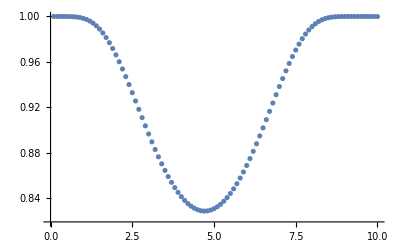

```mathematica
PPlotfirst3= Table[{tVals[[j]],Sum[  Abs[PTab[[k, j]]^2 ] , {k, 1, 3} ] }, {j, 1, Length[tVals]}]  ; 
ListPlot[PPlotfirst3]
```

```mathematica
"Here is the sum of all the probabilities we have computed"
```

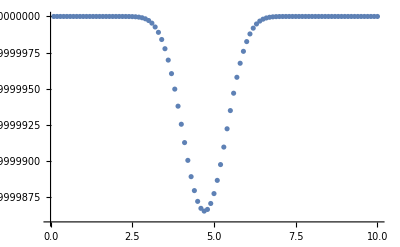

```mathematica
PPlot= Table[{tVals[[j]],Sum[  Abs[PTab[[k, j]]^2 ] , {k, 1, ϕPts} ] }, {j, 1, Length[tVals]}];   ListPlot[PPlot]
```